## Sulman & Gibert Modeling microbe munchers: Trophic interactions control global temperature response of soil carbon stocks Mathematica code

### EQUILIBRIA

```mathematica
Arr[T_,k_,Ea_,T0_]:=k*Exp[-Ea/(8.6*10^-5)(1/(273+T)-1/(273+T0))];
```

```mathematica
eqs2={S-Arr B c==0,
ϵ Arr B c-Subscript[α, P] Arr B P-d B==0,
Subscript[ϵ, P] Subscript[α, P] Arr B P-Subscript[d, P] P==0};
Solve[{S-Arr B c==0 ,
ϵ Arr B c-α1 Arr B P-d B==0 ,
ϵ2 α1 Arr B P-d2 P==0},{B,c,P}]
```

{{B→d2/(Arr α1 ϵ2),c→(S α1 ϵ2)/d2,P→(-d d2+Arr S α1 ϵ ϵ2)/(Arr d2 α1)},{B→(S ϵ)/d,c→d/(Arr ϵ),P→0}}

```mathematica
(* OLD, not needed *)
(*Solve[{S-(Arr1 B c)/(1+Arr1 η c)==0 ,
 ϵ(Arr1 B c)/(1+Arr1 η c)-(α1 Arr2 B P)/(1+α1 Arr2 η2 B)-d B==0 , 
 ϵ2(α2 Arr2 B P)/(1+α2 Arr2 η2 B)-δ P==0},{B,c,P}]*)
```

{{B→(S ϵ)/d,c→d/(Arr1 (ϵ-d η)),P→0},{B→δ/(Arr2 α2 (ϵ2-δ η2)),c→-(-Arr2 S α2 ϵ2+Arr2 S α2 δ η2)/(Arr1 (δ-Arr2 S α2 ϵ2 η+Arr2 S α2 δ η η2)),P→((α2 ϵ2+α1 δ η2-α2 δ η2) (-d δ+Arr2 S α2 ϵ ϵ2-Arr2 S α2 δ ϵ η2))/(Arr2 α1 α2 δ (ϵ2-δ η2))}}

```mathematica
Solve[{S-(Arr1 B c)/(1+Arr1 η c)==0 ,
 ϵ(α1 Arr1 B c)/(1+α1 Arr1 η c)-(α2 Arr2 B P)/(1+α2 Arr2 η2 B)-d B==0 , 
 ϵ2(α2 Arr2 B P)/(1+α2 Arr2 η2 B)-δ P==0},{B,c,P}]
```

{{B→(S α1 ϵ+d S η-d S α1 η)/d,c→d/(Arr1 α1 (ϵ-d η)),P→0},{B→δ/(Arr2 α2 (ϵ2-δ η2)),c→-(-Arr2 S α2 ϵ2+Arr2 S α2 δ η2)/(Arr1 (δ-Arr2 S α2 ϵ2 η+Arr2 S α2 δ η η2)),P→-(ϵ2 (d δ-Arr2 S α1 α2 ϵ ϵ2-Arr2 d S α2 ϵ2 η+Arr2 d S α1 α2 ϵ2 η+Arr2 S α1 α2 δ ϵ η2+Arr2 d S α2 δ η η2-Arr2 d S α1 α2 δ η η2))/(Arr2 α2 (ϵ2-δ η2) (δ-Arr2 S α2 ϵ2 η+Arr2 S α1 α2 ϵ2 η+Arr2 S α2 δ η η2-Arr2 S α1 α2 δ η η2))}}

### FIGURE 2 of main text

```mathematica
(* Equations *)
Arr[T_,k_,Ea_,T0_]:=k*Exp[-Ea/(8.6*10^-5)(1/(273+T)-1/(273+T0))];
eqs={S-(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)==0,
ϵ(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)-(Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B)-d B==0,
Subscript[ϵ, P]((Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B))-Subscript[d, P] P==0};;
eqs2={S-(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)==0,
ϵ(Arr[T,k,Ea,T0] B c)/(1+Arr[T,k,Ea,T0] η c)-(Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B)-d B==0,
Subscript[ϵ, P]((Subscript[α, P] Arr[T,k2,Ea2,T0] B P)/(1+Subscript[α, P] Arr[T,k2,Ea2,T0] Subscript[η, P] B))-Subscript[d, P] P==0};
```

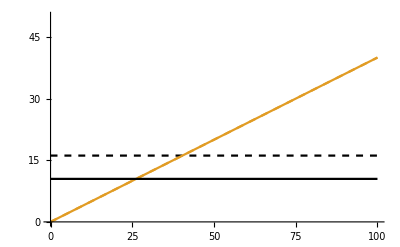

```mathematica
(* Figure 1: PLOTS *)
Plot[{(S ϵ)/d/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0},d/(Arr[T,k,Ea,T0](ϵ-d η))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0},(S ϵ)/d/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0},d/(Arr[T,k,Ea,T0](ϵ-d η))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11,Ea2->0}},{S,0,100},PlotRange->{0,50},AxesStyle->Thickness[0.003], Ticks->{{0,25,50,75,100},{0,15,30,45,60}},PlotStyle->{{ColorData[97,"ColorList"][[2]],Dashed},{Black,Dashed},ColorData[97,"ColorList"][[2]],Black}, TicksStyle->Directive[12]]
```

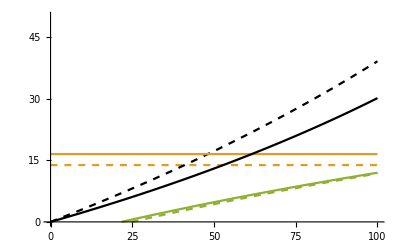

```mathematica
Plot[{δ/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.65},-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.2},-(ϵ2 (d δ-Arr[T,k,Ea2,T0] S α1 α2 ϵ ϵ2-Arr[T,k,Ea2,T0] d S α2 ϵ2 η+Arr[T,k,Ea2,T0] d S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 δ ϵ η2+Arr[T,k,Ea2,T0] d S α2 δ η η2-Arr[T,k,Ea2,T0] d S α1 α2 δ η η2))/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2) (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2-Arr[T,k,Ea2,T0] S α1 α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.2},δ/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.2},-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.2},-(ϵ2 (d δ-Arr[T,k,Ea2,T0] S α1 α2 ϵ ϵ2-Arr[T,k,Ea2,T0] d S α2 ϵ2 η+Arr[T,k,Ea2,T0] d S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 δ ϵ η2+Arr[T,k,Ea2,T0] d S α2 δ η η2-Arr[T,k,Ea2,T0] d S α1 α2 δ η η2))/(Arr[T,k,Ea2,T0] α2 (ϵ2-δ η2) (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α1 α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2-Arr[T,k,Ea2,T0] S α1 α2 δ η η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.2}},{S,0,100},PlotRange->{0,50},AxesStyle->Thickness[0.003], Ticks->{{0,25,50,75,100},{0,15,30,45,60}},PlotStyle->{{ColorData[97,"ColorList"][[2]],Dashed},{Black,Dashed},{ColorData[97,"ColorList"][[3]],Dashed},ColorData[97,"ColorList"][[2]],Black,ColorData[97,"ColorList"][[3]]}, TicksStyle->Directive[12]]
```

### FIGURE 3 of the main text

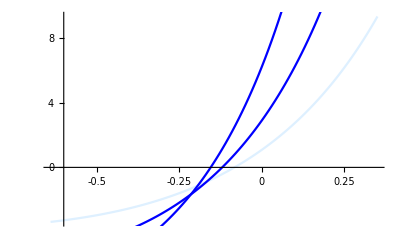

```mathematica
Act=Array[0+0.01# &,100];
(* Against Substrate [not included in the paper] *)
toPlot40=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->24,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->40})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->40})
,{i,Length[Act]}];
toPlot60=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->24,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
toPlot80=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->24,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->80})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->80})
,{i,Length[Act]}];
Plot40=ListLinePlot[Transpose[{Act-0.65,toPlot40}],AxesOrigin->{-0.6,0},PlotStyle->LightBlue,AxesStyle->Thickness[0.003], Ticks->{{-0.5,-0.25,0,0.25},{-4,0,4,8}}, TicksStyle->Directive[12]];
Plot60=ListLinePlot[Transpose[{Act-0.65,toPlot60}],AxesOrigin->{-0.6,0},PlotStyle->Blue];
Plot80=ListLinePlot[Transpose[{Act-0.65,toPlot80}],AxesOrigin->{-0.6,0},PlotStyle->Blue];
Show[Plot40,Plot60,Plot80]
```

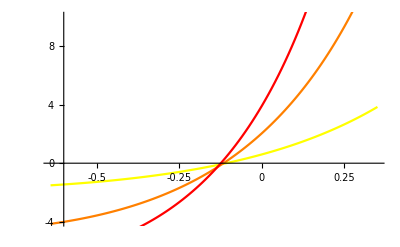

```mathematica
(* Against Substrate [not included in the paper] *)
toPlot21=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->21,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
toPlot23=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->23,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
toPlot25=Table[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->25,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]],S->60})-(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2))/.{T->20,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->Act[[i]], S->60})
,{i,Length[Act]}];
Plot21=ListLinePlot[Transpose[{Act-0.65,toPlot21}],AxesOrigin->{-0.6,0},PlotStyle-> Yellow,AxesStyle->Thickness[0.003], Ticks->{{-0.5,-0.25,0,0.25},{-4,0,4,8}},PlotRange->{-4,10}, TicksStyle->Directive[12]];
Plot23=ListLinePlot[Transpose[{Act-0.65,toPlot23}],AxesOrigin->{-0.6,0},PlotStyle->Orange];
Plot25=ListLinePlot[Transpose[{Act-0.65,toPlot25}],AxesOrigin->{-0.6,0},PlotStyle->Red];
Show[Plot21,Plot23,Plot25]
```

```mathematica
Transpose[{Act-0.65,toPlot21}]
```

{{-0.64,-1.50777},{-0.63,-1.49381},{-0.62,-1.47945},{-0.61,-1.4647},{-0.6,-1.44954},{-0.59,-1.43397},{-0.58,-1.41799},{-0.57,-1.40158},{-0.56,-1.38473},{-0.55,-1.36744},{-0.54,-1.3497},{-0.53,-1.33149},{-0.52,-1.31282},{-0.51,-1.29368},{-0.5,-1.27404},{-0.49,-1.25391},{-0.48,-1.23327},{-0.47,-1.21212},{-0.46,-1.19045},{-0.45,-1.16824},{-0.44,-1.14548},{-0.43,-1.12217},{-0.42,-1.09829},{-0.41,-1.07384},{-0.4,-1.04879},{-0.39,-1.02315},{-0.38,-0.996897},{-0.37,-0.970019},{-0.36,-0.942507},{-0.35,-0.914347},{-0.34,-0.885527},{-0.33,-0.856034},{-0.32,-0.825855},{-0.31,-0.794976},{-0.3,-0.763383},{-0.29,-0.731063},{-0.28,-0.698002},{-0.27,-0.664183},{-0.26,-0.629594},{-0.25,-0.594217},{-0.24,-0.558038},{-0.23,-0.521041},{-0.22,-0.483209},{-0.21,-0.444526},{-0.2,-0.404974},{-0.19,-0.364535},{-0.18,-0.323193},{-0.17,-0.280929},{-0.16,-0.237724},{-0.15,-0.193559},{-0.14,-0.148414},{-0.13,-0.102269},{-0.12,-0.055105},{-0.11,-0.00689954},{-0.1,0.0423684},{-0.09,0.0927207},{-0.08,0.14418},{-0.07,0.196769},{-0.06,0.250511},{-0.05,0.305431},{-0.04,0.361553},{-0.03,0.418902},{-0.02,0.477505},{-0.01,0.537387},{0.,0.598576},{0.01,0.661099},{0.02,0.724986},{0.03,0.790264},{0.04,0.856965},{0.05,0.925119},{0.06,0.994756},{0.07,1.06591},{0.08,1.13861},{0.09,1.2129},{0.1,1.2888},{0.11,1.36636},{0.12,1.44561},{0.13,1.52658},{0.14,1.60932},{0.15,1.69386},{0.16,1.78025},{0.17,1.86853},{0.18,1.95873},{0.19,2.05091},{0.2,2.1451},{0.21,2.24136},{0.22,2.33973},{0.23,2.44026},{0.24,2.54299},{0.25,2.64799},{0.26,2.7553},{0.27,2.86497},{0.28,2.97707},{0.29,3.09164},{0.3,3.20876},{0.31,3.32847},{0.32,3.45083},{0.33,3.57593},{0.34,3.70381},{0.35,3.83454}}

### Figure 3 B:

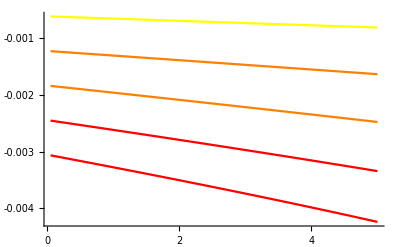

```mathematica
Act=Array[14.95+0.05# &,101];
toPlot02=Table[(8.6*10^-5*Log[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2)))/(-(-Arr[15,k,Ea2,T0] S α2 ϵ2+Arr[15,k,Ea2,T0]S α2 δ η2)/(Arr[20,k,Ea,T0] (δ-Arr[15,k,Ea2,T0] S α2 ϵ2 η+Arr[15,k,Ea2,T0] S α2 δ η η2)))/.{T->Act[[i]],S->60,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.2}]*(1/(1/T-1/15))/.{T->Act[[i]]})-8.6*10^-5*Log[((d/(Arr[T,k,Ea,T0](ϵ-d η)))/(d/(Arr[20,k,Ea,T0](ϵ-d η))))/.{T->Act[[i]],T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11}]*(1/(1/T-1/15))/.{T->Act[[i]]}
,{i,Length[Act]}];
toPlot04=Table[(8.6*10^-5*Log[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2)))/(-(-Arr[15,k,Ea2,T0] S α2 ϵ2+Arr[15,k,Ea2,T0]S α2 δ η2)/(Arr[20,k,Ea,T0] (δ-Arr[15,k,Ea2,T0] S α2 ϵ2 η+Arr[15,k,Ea2,T0] S α2 δ η η2)))/.{T->Act[[i]],S->60,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.4}]*(1/(1/T-1/15))/.{T->Act[[i]]})-8.6*10^-5*Log[((d/(Arr[T,k,Ea,T0](ϵ-d η)))/(d/(Arr[20,k,Ea,T0](ϵ-d η))))/.{T->Act[[i]],T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11}]*(1/(1/T-1/15))/.{T->Act[[i]]}
,{i,Length[Act]}];
toPlot65=Table[(8.6*10^-5*Log[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2)))/(-(-Arr[15,k,Ea2,T0] S α2 ϵ2+Arr[15,k,Ea2,T0]S α2 δ η2)/(Arr[20,k,Ea,T0] (δ-Arr[15,k,Ea2,T0] S α2 ϵ2 η+Arr[15,k,Ea2,T0] S α2 δ η η2)))/.{T->Act[[i]],S->60,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.60}]*(1/(1/T-1/15))/.{T->Act[[i]]})-8.6*10^-5*Log[((d/(Arr[T,k,Ea,T0](ϵ-d η)))/(d/(Arr[20,k,Ea,T0](ϵ-d η))))/.{T->Act[[i]],T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11}]*(1/(1/T-1/15))/.{T->Act[[i]]}
,{i,Length[Act]}];
toPlot1=Table[(8.6*10^-5*Log[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2)))/(-(-Arr[15,k,Ea2,T0] S α2 ϵ2+Arr[15,k,Ea2,T0]S α2 δ η2)/(Arr[20,k,Ea,T0] (δ-Arr[15,k,Ea2,T0] S α2 ϵ2 η+Arr[15,k,Ea2,T0] S α2 δ η η2)))/.{T->Act[[i]],S->60,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->0.8}]*(1/(1/T-1/15))/.{T->Act[[i]]})-8.6*10^-5*Log[((d/(Arr[T,k,Ea,T0](ϵ-d η)))/(d/(Arr[20,k,Ea,T0](ϵ-d η))))/.{T->Act[[i]],T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11}]*(1/(1/T-1/15))/.{T->Act[[i]]}
,{i,Length[Act]}];
toPlot2=Table[(8.6*10^-5*Log[(-(-Arr[T,k,Ea2,T0] S α2 ϵ2+Arr[T,k,Ea2,T0]S α2 δ η2)/(Arr[T,k,Ea,T0] (δ-Arr[T,k,Ea2,T0] S α2 ϵ2 η+Arr[T,k,Ea2,T0] S α2 δ η η2)))/(-(-Arr[15,k,Ea2,T0] S α2 ϵ2+Arr[15,k,Ea2,T0]S α2 δ η2)/(Arr[20,k,Ea,T0] (δ-Arr[15,k,Ea2,T0] S α2 ϵ2 η+Arr[15,k,Ea2,T0] S α2 δ η η2)))/.{T->Act[[i]],S->60,T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α1->2,k2->0.11,Ea2->1}]*(1/(1/T-1/15))/.{T->Act[[i]]})-8.6*10^-5*Log[((d/(Arr[T,k,Ea,T0](ϵ-d η)))/(d/(Arr[20,k,Ea,T0](ϵ-d η))))/.{T->Act[[i]],T0->15,k->0.11,Ea->0.65, η->0.04, ϵ->0.4,d->1,ϵ2->0.2,η2->0.04,δ->0.8,α2->2,α->2,k2->0.11}]*(1/(1/T-1/15))/.{T->Act[[i]]}
,{i,Length[Act]}];
Plot02=ListLinePlot[Transpose[{Act-15,toPlot02}],AxesOrigin->{0,0},PlotStyle-> Yellow,AxesStyle->Thickness[0.003], Ticks->{{0,1,2,3,4,5},{0,-0.001,-0.002,-0.003,-0.004,-0.005}},PlotRange->{{0,5},{0,-0.005}}, TicksStyle->Directive[12]];
Plot04=ListLinePlot[Transpose[{Act-15,toPlot04}],AxesOrigin->{0,0},PlotStyle->Orange];
Plot65=ListLinePlot[Transpose[{Act-15,toPlot65}],AxesOrigin->{0,0},PlotStyle->Orange];
Plot1=ListLinePlot[Transpose[{Act-15,toPlot1}],AxesOrigin->{-0.6,0},PlotStyle->Red];
Plot2=ListLinePlot[Transpose[{Act-15,toPlot2}],AxesOrigin->{-0.6,0},PlotStyle->Red];
Show[Plot02,Plot04,Plot65,Plot1,Plot2]
```